EXTERNAL DEPENDENCIES: Evaluate the setups in model-setup.nb and shere-LSA-setup.nb first

```mathematica
fixedParams={
r->3.5,Dm["md"]->0.2,Dm[_]->0.01,DD->11,DG->11,DF->11,DB->11
};
```

```mathematica
Vol=4Pi/3 3.5^3;
```

```mathematica
densitiesWT={nD->8690/Vol,nG->2170/Vol,nB->1037/Vol,nF->934/Vol};
```

## Parameter set filtered with all constraints except Cdc42-psy1^TM

```mathematica
roundSignificant[x_,digits_Integer]:=N@Round[x,10^(Floor[Log10@x]-digits+1)];
```

Selected parameter set from parameter sampling and filtering performed in parameter-sampling.nb

```mathematica
selectedParams=Thread[sampleParamNames->roundSignificant[selectedParams,2]]
```

{ktg→0.053,kgt→0.35,kD→0.015,kdoff→0.22,kfd→0.0077,kbfD→0.025,ktD→0.17,ktB→0.68,kb→0.032,kbF→0.29,kbf→0.25,kF→0.43,kf→0.26}

```mathematica
selectedParams={ktg->0.053,kgt->0.35,kD->0.015,kdoff->0.22,kfd->0.0077,kbfD->0.025,ktD->0.17,ktB->0.68,kb->0.032,kbF->0.29,kbf->0.25,kF->0.43,kf->0.26};
```

```mathematica
defaultParams=Join[
fixedParams,
densitiesWT,
selectedParams
];
```

```mathematica
nSolveUniformEq@defaultParams
```

{{mt→8.02616,md→34.6294,mg→6.36302,mtg→7.73356,mb→3.24556,mbf→3.46872,mf→1.52376,cD→5.19618,cB→0.0190293,cF→0.921343}}

### Dispersion relation example(s)

```mathematica
testParams=Join[
fixedParams,
densitiesWT,
Thread[sampleParamNames->selectedParams]
];
```

```mathematica
wtDispRel=With[{params=defaultParams},Join[{
{0,findHomEV[
params,
First@nSolveUniformEq@params,
"ApproxJacobian"->sphereJacobianApprox
]}
},
findDispRel[
params,
First@nSolveUniformEq@params,
7,"ApproxJacobian"->sphereJacobianApprox
][[2;;-1]]
]];
```

```mathematica
findHomEV[defaultParams,
First@nSolveUniformEq@defaultParams,
"ApproxJacobian"->sphereJacobianApprox
]
```

-0.198807+0. ⅈ

```mathematica
wtDispRel
```

{{0,-0.198807+0. ⅈ},{1,0.0342915+0. ⅈ},{2,0.0282413+0. ⅈ},{3,0.0174014},{4,0.00595208},{5,-0.00562037-8.19505×10^-22 ⅈ},{6,-0.0177032+1.60283×10^-21 ⅈ},{7,-0.0306877-1.48279×10^-21 ⅈ}}

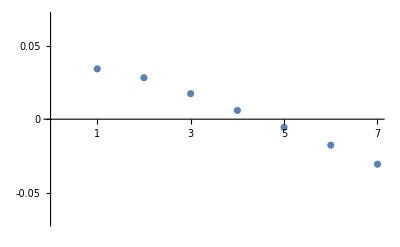

```mathematica
ListPlot[wtDispRel,
PlotRange->{-0.07,0.07},
Ticks->{Range[7],{-0.05,0,0.05}},
AxesStyle->Black
]
```

### Parameter sweeps in (n_D,n_G) parameter plane

```mathematica
20000/Vol
```

111.362

```mathematica
4000/Vol
```

22.2724

```mathematica
nDRange=Range[0,20000/Vol,1];
nGRange=Range[0,4000/Vol,0.2];
```

```mathematica
frameStyle={
AspectRatio->1,
PlotRange->{MinMax@nDRange,MinMax@nGRange},
Frame->True,FrameStyle->Directive[Black,FontSize->14],
FrameTicks->{{
{{0,0,{0,0.015}},{#/2,Rotate["N_(<G>)",Pi/2],0},{#,4000,{0,0.015}}}&@Max@nGRange,None
},{
{{0,0,{0,0.015}},{#/2,"N_(<D>)",0},{#,20000,{0,0.015}}}&@Max@nDRange,None
}
}
};
```

#### WT

```mathematica
sweepParams=Join[defaultParams];
```

```mathematica
densitiesWT
```

{nD→48.3868,nG→12.0828,nB→5.77412,nF→5.20061}

```mathematica
locEqsTable[nD,nG,"WT"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{66.4301,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"WT"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"WT"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100},{0,-100},{0,-100}}}
]
]&,
locEqsTable[nD,nG,"WT"],{2}
];//AbsoluteTiming
```

{5.74303,Null}

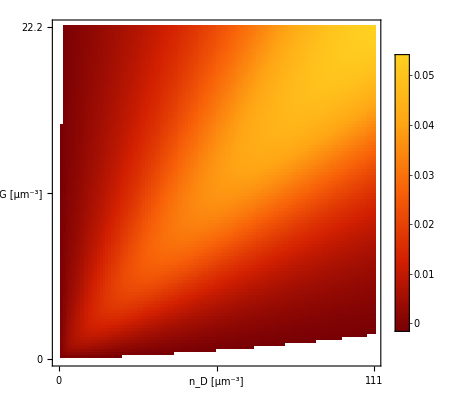

```mathematica
ArrayPlot[
Reverse@Transpose@Map[
Re@#[[3,2,2]]&,
dispRelTable[nD,nG,"WT"],
{2}
],
PlotLegends->Automatic,
AspectRatio->1,
ColorFunction->"SolarColors",
PlotRange->{0,All},
Frame->True,FrameStyle->Directive[Black,FontSize->14],
DataRange->{MinMax@nDRange,MinMax@nGRange},
FrameTicks->{{
{{0,0,{0,0.015}},{Max@nGRange/2,Rotate["n_(<G>) [μm^-3]",Pi/2],0},{#,#,{0,0.015}}&@Max@nGRange},None
},{
{{0,0,{0,0.015}},{Max@nDRange/2,"n_(<D>) [μm^-3]",0},{#,#,{0,0.015}}&@Max@nDRange},None
}
}
]
```

```mathematica
Graphics[{
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0.3,0.7,0.1},{1,1,1}]&,
dispRelTable[nD,nG,"WT"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
AbsolutePointSize[12],White,Point[{nD,nG}/.densitiesWT],
AbsolutePointSize[8],Black,Point[{nD,nG}/.densitiesWT]
},
Sequence@@frameStyle
]
```

-Graphics-

#### bem1Δ

```mathematica
sweepParams=Join[{nB->0},defaultParams];
```

```mathematica
locEqsTable[nD,nG,"Bem1d"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{65.3296,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"Bem1d"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"Bem1d"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
Quiet@findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100}}}
]
]&,
locEqsTable[nD,nG,"Bem1d"],{2}
];//AbsoluteTiming
```

{5.37333,Null}

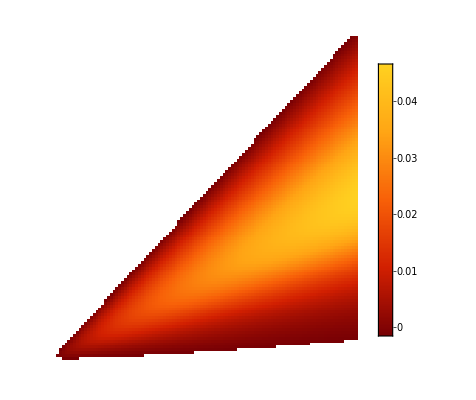

```mathematica
ArrayPlot[
Reverse@Transpose@Map[
Re@#[[3,2,2]]&,
dispRelTable[nD,nG,"Bem1d"],
{2}
],
PlotLegends->Automatic,
AspectRatio->1,
FrameTicks->Automatic,
PlotRange->{0,All},
ColorFunction->"SolarColors"
]
```

```mathematica
Graphics[{
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0,0.5,0.8},{1,1,1}]&,
dispRelTable[nD,nG,"Bem1d"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
AbsolutePointSize[8],Black,Point[{nD,nG}/.densitiesWT],
AbsolutePointSize[12],White,Point[{nD,nG-599/Vol}/.densitiesWT],
AbsolutePointSize[8],Darker@Green,Point[{nD,nG-599/Vol}/.densitiesWT],
AbsolutePointSize[12],White,Point[{1.5nD,nG}/.densitiesWT],
AbsolutePointSize[8],Darker@Green,Point[{1.5nD,nG}/.densitiesWT],
AbsolutePointSize[8],Red,Point[{0.5nD,nG-599/Vol}/.densitiesWT],
AbsolutePointSize[12],White,Point[{nD,nG-(1100+599)/Vol}/.densitiesWT],
AbsolutePointSize[8],Darker@Green,Point[{nD,nG-(1100+599)/Vol}/.densitiesWT],
},
Sequence@@frameStyle
]
```

-Graphics-

#### bem1Δ, 2-fold GEF activity

```mathematica
sweepParams=Join[{nB->0,kfd->(2kfd/.defaultParams)},defaultParams];
```

```mathematica
locEqsTable[nD,nG,"Bem1d,GEF+"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{58.7095,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"Bem1d,GEF+"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"Bem1d,GEF+"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100}}}
]
]&,
locEqsTable[nD,nG,"Bem1d,GEF+"],{2}
];//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{4.64161,Null}

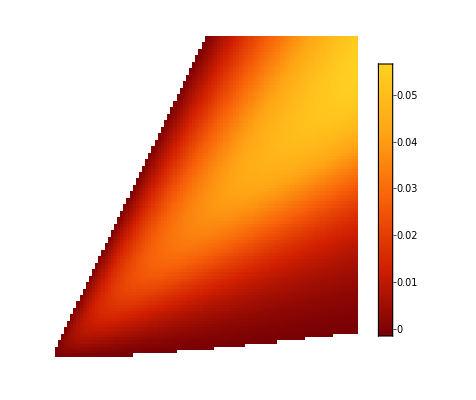

```mathematica
ArrayPlot[
Reverse@Transpose@Map[
Re@#[[3,2,2]]&,
dispRelTable[nD,nG,"Bem1d,GEF+"],
{2}
],
PlotLegends->Automatic,
AspectRatio->1,
FrameTicks->Automatic,
PlotRange->{0,All},
ColorFunction->"SolarColors"
]
```

```mathematica
Graphics[{
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0,0.7,0.9},{1,1,1}]&,
dispRelTable[nD,nG,"Bem1d,GEF+"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0,0.5,0.8,1},{0,0,0,0}]&,
dispRelTable[nD,nG,"Bem1d"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
AbsolutePointSize[12],White,Point[{nD,nG}/.densitiesWT],
AbsolutePointSize[8],Darker@Black,Point[{nD,nG}/.densitiesWT]
},
Sequence@@frameStyle
]
```

-Graphics-

#### Cdc42-ritC

```mathematica
sweepParams=Join[{kdoff->0},defaultParams];
```

```mathematica
locEqsTable[nD,nG,"Cdc42-ritC"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{2.70151,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"Cdc42-ritC"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"Cdc42-ritC"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100},{0,-100},{0,-100}}}
]
]&,
locEqsTable[nD,nG,"Cdc42-ritC"],{2}
];//AbsoluteTiming
```

{0.285411,Null}

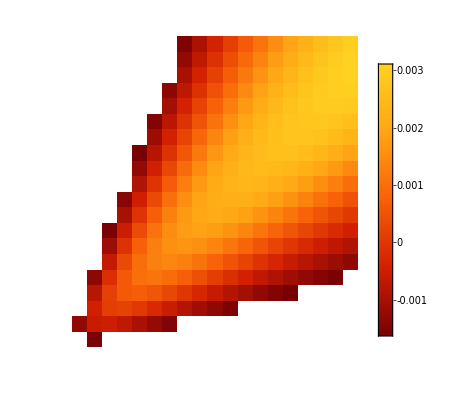

```mathematica
ArrayPlot[
Reverse@Transpose@Map[
Re@#[[3,2,2]]&,
dispRelTable[nD,nG,"Cdc42-ritC"],
{2}
],
PlotLegends->Automatic,
AspectRatio->1,
FrameTicks->Automatic,
PlotRange->{0,All},
ColorFunction->"SolarColors"
]
```

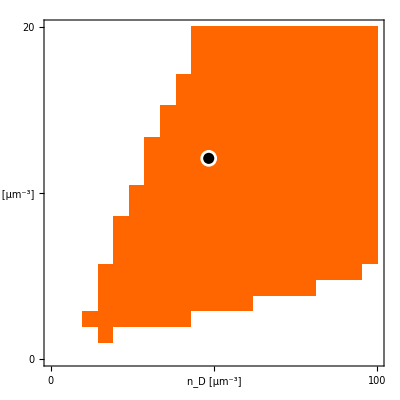

```mathematica
Graphics[{
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{1,0.4,0},{1,1,1}]&,
dispRelTable[nD,nG,"Cdc42-ritC"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
AbsolutePointSize[12],White,Point[{nD,nG}/.densitiesWT],
AbsolutePointSize[8],Darker@Black,Point[{nD,nG}/.densitiesWT]
},
Sequence@@frameStyle
]
```

### 5-fold GAP range

```mathematica
nDRange=Range[0,20000/Vol,1];
nGRange=Range[0,20000/Vol,1];
```

```mathematica
frameStyle={
AspectRatio->1,
PlotRange->{MinMax@nDRange,MinMax@nGRange},
Frame->True,FrameStyle->Directive[Black,FontSize->14],
FrameTicks->{{
{{0,0,{0,0.015}},{#/2,Rotate["N_(<G>)",Pi/2],0},{#,20000,{0,0.015}}}&@Max@nGRange,None
},{
{{0,0,{0,0.015}},{#/2,"N_(<D>)",0},{#,20000,{0,0.015}}}&@Max@nDRange,None
}
}
};
```

#### WT

```mathematica
sweepParams=Join[defaultParams];
```

```mathematica
densitiesWT
```

{nD→48.3868,nG→12.0828,nB→5.77412,nF→5.20061}

```mathematica
locEqsTable[nD,nG,"WT"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{66.7938,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"WT"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"WT"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100},{0,-100},{0,-100}}}
]
]&,
locEqsTable[nD,nG,"WT"],{2}
];//AbsoluteTiming
```

{5.58164,Null}

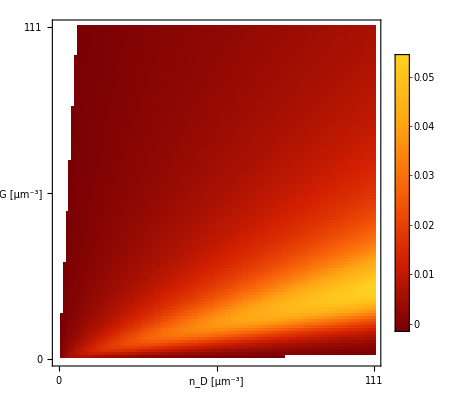

```mathematica
ArrayPlot[
Reverse@Transpose@Map[
Re@#[[3,2,2]]&,
dispRelTable[nD,nG,"WT"],
{2}
],
PlotLegends->Automatic,
AspectRatio->1,
ColorFunction->"SolarColors",
PlotRange->{0,All},
Frame->True,FrameStyle->Directive[Black,FontSize->14],
DataRange->{MinMax@nDRange,MinMax@nGRange},
FrameTicks->{{
{{0,0,{0,0.015}},{Max@nGRange/2,Rotate["n_(<G>) [μm^-3]",Pi/2],0},{#,#,{0,0.015}}&@Max@nGRange},None
},{
{{0,0,{0,0.015}},{Max@nDRange/2,"n_(<D>) [μm^-3]",0},{#,#,{0,0.015}}&@Max@nDRange},None
}
}
]
```

```mathematica
Graphics[{
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0.3,0.7,0.1},{1,1,1}]&,
dispRelTable[nD,nG,"WT"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
AbsolutePointSize[12],White,Point[{nD,nG}/.densitiesWT],
AbsolutePointSize[8],Black,Point[{nD,nG}/.densitiesWT]
},
Sequence@@frameStyle
]
```

-Graphics-

#### bem1Δ

```mathematica
sweepParams=Join[{nB->0},defaultParams];
```

```mathematica
locEqsTable[nD,nG,"Bem1d"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{66.6142,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"Bem1d"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"Bem1d"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
Quiet@findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100}}}
]
]&,
locEqsTable[nD,nG,"Bem1d"],{2}
];//AbsoluteTiming
```

{5.22881,Null}

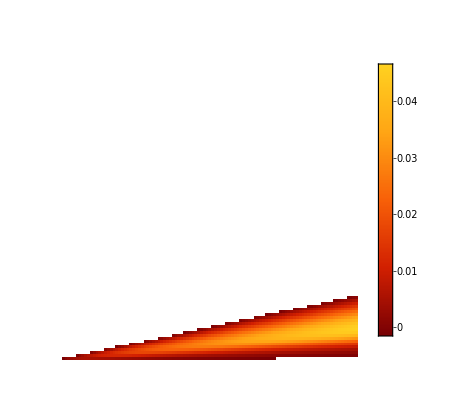

```mathematica
ArrayPlot[
Reverse@Transpose@Map[
Re@#[[3,2,2]]&,
dispRelTable[nD,nG,"Bem1d"],
{2}
],
PlotLegends->Automatic,
AspectRatio->1,
FrameTicks->Automatic,
PlotRange->{0,All},
ColorFunction->"SolarColors"
]
```

```mathematica
Graphics[{
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0,0.5,0.8},{1,1,1}]&,
dispRelTable[nD,nG,"Bem1d"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
]
},
Sequence@@frameStyle
]
```

-Graphics-

#### bem1Δ, 2-fold GEF activity

```mathematica
sweepParams=Join[{nB->0,kfd->(2kfd/.defaultParams)},defaultParams];
```

```mathematica
locEqsTable[nD,nG,"Bem1d,GEF+"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{65.4826,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"Bem1d,GEF+"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"Bem1d,GEF+"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100}}}
]
]&,
locEqsTable[nD,nG,"Bem1d,GEF+"],{2}
];//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{5.22772,Null}

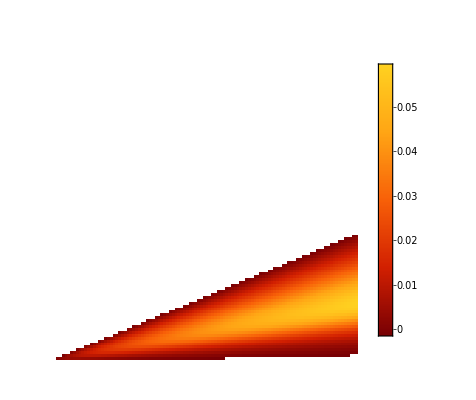

```mathematica
ArrayPlot[
Reverse@Transpose@Map[
Re@#[[3,2,2]]&,
dispRelTable[nD,nG,"Bem1d,GEF+"],
{2}
],
PlotLegends->Automatic,
AspectRatio->1,
FrameTicks->Automatic,
PlotRange->{0,All},
ColorFunction->"SolarColors"
]
```

```mathematica
Graphics[{
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0,0.7,0.9},{1,1,1}]&,
dispRelTable[nD,nG,"Bem1d,GEF+"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0,0.5,0.8,1},{0,0,0,0}]&,
dispRelTable[nD,nG,"Bem1d"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
]
},
Sequence@@frameStyle
]
```

-Graphics-

## Cdc42-psy1^TM

Selected parameter set from parameter sampling and filtering performed in parameter-sampling.nb

```mathematica
selectedParams={ktg->0.36,kgt->1.5,kD->0.0017,kdoff->0.82,kfd->0.052,kbfD->0.3,ktD->1.,ktB->2.1,kb->0.23,kbF->0.057,kbf->0.03,kF->0.017,kf->0.046};
```

```mathematica
defaultParams=Join[
fixedParams,
densitiesWT,
selectedParams
];
```

#### WT

```mathematica
sweepParams=Join[defaultParams];
```

```mathematica
locEqsTable[nD,nG,"TM-set,WT"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{59.9247,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"TM-set,WT"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"TM-set,WT"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100},{0,-100},{0,-100}}}
]
]&,
locEqsTable[nD,nG,"TM-set,WT"],{2}
];//AbsoluteTiming
```

{5.34545,Null}

```mathematica
Graphics[
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0.3,0.7,0.1},{1,1,1}]&,
dispRelTable[nD,nG,"TM-set,WT"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
Sequence@@frameStyle
]
```

-Graphics-

#### bem1Δ

```mathematica
sweepParams=Join[{nB->0},defaultParams];
```

```mathematica
locEqsTable[nD,nG,"TM-set,Bem1d"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{59.5539,Null}

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"TM-set,Bem1d"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

-Graphics-

```mathematica
dispRelTable[nD,nG,"TM-set,Bem1d"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100}}}
]
]&,
locEqsTable[nD,nG,"TM-set,Bem1d"],{2}
];//AbsoluteTiming
```

{5.00653,Null}

```mathematica
Graphics[
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0,0.5,0.8},{1,1,1}]&,
dispRelTable[nD,nG,"TM-set,Bem1d"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
Sequence@@frameStyle
]
```

-Graphics-

#### Cdc42-TM

```mathematica
sweepParams=Join[{kdoff->0,Dm["md"]->0.0025,Dm["mt"]->0.0025,Dm["mtg"]->0.0025,
Dm["mb"]->0.0025,Dm["mbf"]->0.0025},defaultParams];
```

```mathematica
locEqsTable[nD,nG,"TM-set,Cdc42-TM"]=ParallelTable[
{
{nDIter,nGIter},
nSolveUniformEq[Join[{nD->nDIter,nG->nGIter},sweepParams]][[All,All,2]]
},
{nDIter,nDRange},{nGIter,nGRange}
];//AbsoluteTiming
```

{58.9191,Null}

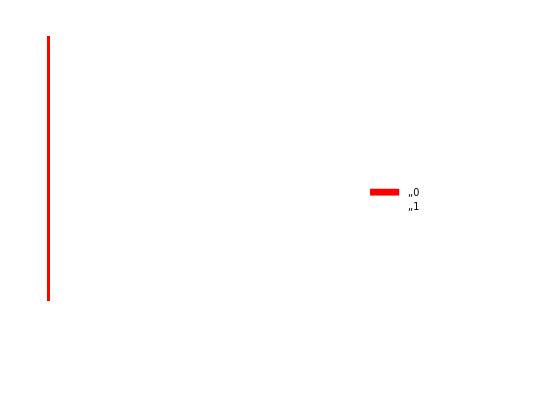

```mathematica
ArrayPlot[
Reverse@Transpose@Map[Length@#[[2]]&,locEqsTable[nD,nG,"TM-set,Cdc42-TM"],{2}],
PlotLegends->Automatic,
AspectRatio->1,
ColorRules->{3->Black,2->Gray,1->White,0->Red},
ImageSize->Tiny
]
```

```mathematica
dispRelTable[nD,nG,"TM-set,Cdc42-TM"]=ParallelMap[Join[
#,
If[Length@#[[2]]>0,
{
findDispRel[
Join[Thread[{nD,nG}->#[[1]]],sweepParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
2,"ApproxJacobian"->sphereJacobianApprox
]
},
{{{0,-100},{0,-100},{0,-100}}}
]
]&,
locEqsTable[nD,nG,"TM-set,Cdc42-TM"],{2}
];//AbsoluteTiming
```

{4.87893,Null}

```mathematica
Graphics[
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{1,0.4,0},{1,1,1}]&,
dispRelTable[nD,nG,"TM-set,Cdc42-TM"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
Sequence@@frameStyle
]
```

-Graphics-

```mathematica
Graphics[{
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{1,0.4,0},{1,1,1}]&,
dispRelTable[nD,nG,"TM-set,Cdc42-TM"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
],
Raster[Transpose@Map[
If[Re@#[[3,2,2]]>0,{0,0.5,0.8,1},{1,1,1,0}]&,
dispRelTable[nD,nG,"TM-set,Bem1d"],
{2}
],
Transpose@{MinMax@nDRange,MinMax@nGRange}
]
},
Sequence@@frameStyle
]
```

-Graphics-